```mathematica
ClearAll["`*"]
L=1;m^2=-2;
SetDirectory[NotebookDirectory[]];
```

## eigen equation

```mathematica
vars={t,r,x,y};xa[μ_]:=vars⟦μ⟧;dim=Length[vars];
f[r_]:=1-(1+(e mu^2)/(4 zh^2)) (1-r^2)^3+(e mu^2)/(4 zh^2)(1-r^2)^4;
ds^2=zh^2/((1-r^2)^2)(-f[r] Dt[t]^2+(4 r^2 Dt[r]^2)/(zh^2 f[r])+Dt[x]^2+Dt[y]^2);
coematrix=Coefficient[ds^2,Dt[vars]⊗Dt[vars]];
metric=1/2 Simplify[coematrix+DiagonalMatrix[Diagonal[coematrix]]];
gbb[μ_,ν_]:=metric⟦μ,ν⟧;
invmetric=Simplify[Inverse[metric]];
gaa[μ_,ν_]:=invmetric⟦μ,ν⟧;
g=Simplify[Det[metric]];
(*Γabb[λ_,μ_,ν_]:=Simplify[∑_(σ=1)^dim 1/2 gaa[λ,σ] (-∂_xa[σ] gbb[μ,ν]+∂_xa[μ] gbb[ν,σ]+∂_xa[ν] gbb[σ,μ])];*)
(*ansatz for scalar field*)
Φ=((1-r^2)/zh) ϕ[r];
A={mu r^2,0,0,0};
Ab[μ_]:=A⟦μ⟧;Aa[ν_]:=∑_(σ=1)^dim gaa[σ,ν] Ab[σ];
DΦb[μ_]:=D[Φ, xa[μ]]-ⅈ Ab[μ]Φ;
scalar=Simplify[1/(√-g)∑_(μ=1)^dim (D[#, xa[μ]]-ⅈ Ab[μ]#&[√-g ∑_(ν=1)^dim gaa[μ,ν] DΦb[ν]])-m^2 Φ];
nonfactor[eqs_]:=Block[{First,Last,FactorList},SetAttributes[{First,Last,FactorList},Listable];Simplify[First[Last[FactorList[eqs]]]]];
eqs=Simplify[nonfactor[scalar]];
jacobi=Simplify[Coefficient[(eqs/.{Derivative[i_][h_][r]->Subscript[dr, i] h[r],h_[r]->eye h[r]}),ϕ[r]]];
Simplify[Collect[jacobi,zh]]
subeqs=eqs/.{Derivative[i_][h_][r]:>D[(Series[h[r],{r,0,3}]), {r,i}],h_[r]:>Series[h[r],{r,0,3}]};
```

4 e^2 eye mu^4 r (-1+r^2)^4 (-1+2 r^2)+e^2 mu^4 (-1+r^2)^5 (-1+7 r^2) dr_1+e^2 mu^4 r (-1+r^2)^6 dr_2+16 (3-3 r^2+r^4) zh^4 (4 eye r (-1+r^2)+(3-9 r^2+5 r^4) dr_1+r (3-3 r^2+r^4) dr_2)+8 mu^2 zh^2 (8 eye r^3+2 e eye r (4-16 r^2+22 r^4-13 r^6+3 r^8)+3 e (-1+r^2)^2 (-1+6 r^2-6 r^4+2 r^6) dr_1+e r (-1+r^2)^3 (3-3 r^2+r^4) dr_2)

```mathematica
Simplify[SeriesCoefficient[subeqs,{r,0,0}]]
Simplify[SeriesCoefficient[eqs,{r,0,0}]]
X=Simplify[Coefficient[jacobi,zh^4]]
Y=Simplify[Coefficient[jacobi,zh^2]]
Z=Simplify[jacobi/.zh->0]
```

(e mu^2-12 zh^2)^2 ϕ'[0]

(e mu^2-12 zh^2)^2 ϕ'[0]

16 (3-3 r^2+r^4) (4 eye r (-1+r^2)+(3-9 r^2+5 r^4) dr_1+r (3-3 r^2+r^4) dr_2)

8 mu^2 (8 eye r^3+2 e eye r (4-16 r^2+22 r^4-13 r^6+3 r^8)+3 e (-1+r^2)^2 (-1+6 r^2-6 r^4+2 r^6) dr_1+e r (-1+r^2)^3 (3-3 r^2+r^4) dr_2)

e^2 mu^4 (-1+r^2)^4 (4 eye r (-1+2 r^2)+(1-8 r^2+7 r^4) dr_1+r (-1+r^2)^2 dr_2)

## eigenvalue

```mathematica
Nr=56;Lr=1;mu=5.6;e=1/2.4106577477353315;
(*Chebshev谱求导矩阵生成函数*)
chebp[n_]:=Table[Cos[(i π)/(n-1.0)],{i,0,n-1}];
cheb[n_,l_]:=Module[{x,c,sdm},x=chebp[n];c=Table[If[i==1||i==n,2.0,1.0],{i,1,n}];sdm=2/l Table[If[i≠j,c[[i]]/c[[j]](-1)^(i+j)/(x[[i]]-x[[j]]),0],{i,1,n},{j,1,n}];sdm-=DiagonalMatrix[Total[sdm,{2}]]];
Eye=IdentityMatrix[Nr];Zero=ConstantArray[0,{Nr,Nr}];
gridr=0.5(chebp[Nr]+1);
dr=cheb[Nr,Lr];drs[1]=dr;drs[2]=dr.dr;
{Xm,Ym,Zm}={X,Y,Z}/.{Subscript[dr, i_]->drs[i],eye->Eye,r-> gridr};
Xm⟦1⟧=Zero⟦1⟧;Xm⟦-1⟧=Zero⟦-1⟧;
Ym⟦1⟧=Zero⟦1⟧;Ym⟦-1⟧=Zero⟦-1⟧;
Zm⟦1⟧=Eye⟦1⟧;Zm⟦-1⟧=dr⟦-1⟧;
left=ArrayFlatten[{{-Ym,-Zm},{Eye,Zero}}];
right=ArrayFlatten[{{Xm,Zero},{Zero,Eye}}];
EV=Chop[Eigenvalues[{left,right}]]
EVmax=Max[Abs[DeleteCases[DeleteCases[EV,∞],ComplexInfinity]]]
1/mu(zh/(4π)(3- (e mu^2)/(4 zh^2)))/.zh->√EVmax
```

{ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,2.48094,1.15317,1.08675,1.08417,1.08408+1.06566×10^-6 ⅈ,1.08408-1.06566×10^-6 ⅈ,1.08407,1.08402,1.08395,1.08384,1.08355,1.0834,1.0827,1.08254,1.08118,1.08107,1.07889,1.07864,1.07561,1.07498,1.07105,1.06987,1.06494,1.06303,1.05704,1.05418,1.04706,1.04306,1.03475,1.02944,1.01987,1.01308,1.0022,0.993814,0.981544,0.971479,0.957745,0.945996,0.930685,0.917294,0.900313,0.885405,0.866615,0.850373,0.829663,0.812356,0.789575,0.771525,0.746564,0.728174,0.700898,0.682604,0.652942,0.635239,0.603114,0.586497,0.551926,0.536915,0.499934,0.486999,0.44777,0.437357,0.396088,0.388541,0.345587,0.341171,0.29696,0.295766,0.252939,0.250842,0.21305,0.207914,0.176561,0.168699,0.143721,0.133628,0.11475,0.103013,0.0896756,0.076993,0.0684774,0.0555482,0.0509517,0.0384764,0.0368599,0.0258457,0.0253995,0.0174788,0.0158778,0.0113444,0.00928968,0.00702628,0.00502118,0.00409721,0.00246557,0.00221728,0.00108401,0.00105532,0.000416799,0.000399831,0.000124715,0.0000718982,0.0000302022,5.27652×10^-6,5.83881×10^-7,3.12176×10^-8,4.0539×10^-10,0}

2.48094

0.0378068

```mathematica
1/mu(zh/(4π)(3- (e mu^2)/(4 zh^2)))/.zh->√47.65506351021689
```

0.149045

## data

### data1

```mathematica
Clear[e];
Nr=66;Lr=1;mu=5.6;et1={};normet1={};
(*Chebshev谱求导矩阵生成函数*)
chebp[n_]:=Table[Cos[(i π)/(n-1.0)],{i,0,n-1}];
cheb[n_,l_]:=Module[{x,c,sdm},x=chebp[n];c=Table[If[i==1||i==n,2.0,1.0],{i,1,n}];sdm=2/l Table[If[i≠j,c[[i]]/c[[j]](-1)^(i+j)/(x[[i]]-x[[j]]),0],{i,1,n},{j,1,n}];sdm-=DiagonalMatrix[Total[sdm,{2}]]];
Eye=IdentityMatrix[Nr];Zero=ConstantArray[0,{Nr,Nr}];
gridr=0.5(chebp[Nr]+1);
dr=cheb[Nr,Lr];drs[1]=dr;drs[2]=dr.dr;
Do[{Xm,Ym,Zm}={X,Y,Z}/.{Subscript[dr, i_]->drs[i],eye->Eye,r-> gridr};
Xm⟦1⟧=Zero⟦1⟧;Xm⟦-1⟧=Zero⟦-1⟧;
Ym⟦1⟧=Zero⟦1⟧;Ym⟦-1⟧=Zero⟦-1⟧;
Zm⟦1⟧=dr⟦1⟧;Zm⟦-1⟧=dr⟦-1⟧;
left=ArrayFlatten[{{-Ym,-Zm},{Eye,Zero}}];
right=ArrayFlatten[{{Xm,Zero},{Zero,Eye}}];
EV=Chop[Eigenvalues[{left,right}]];
EVmax=Max[Abs[DeleteCases[DeleteCases[EV,Infinity],ComplexInfinity]]];
AppendTo[et1,{e,1/mu(zh/(4π)(3- (e mu^2)/(4 zh^2)))/.zh->√EVmax}];
AppendTo[normet1,{e,1/((0.2131)mu)(zh/(4π)(3- (e mu^2)/(4 zh^2)))/.zh->√EVmax}],{e,0.05,1,0.05}]
```

```mathematica
TcO1=Prepend[et1,{0.,0.2131}]
nTcO1=Prepend[normet1,{0.,1.}]
```

{{0.,0.2131},{0.05,0.212418},{0.1,0.211771},{0.15,0.211128},{0.2,0.21049},{0.25,0.209857},{0.3,0.209229},{0.35,0.208606},{0.4,0.207987},{0.45,0.207374},{0.5,0.206764},{0.55,0.20616},{0.6,0.20556},{0.65,0.204964},{0.7,0.204374},{0.75,0.203787},{0.8,0.203205},{0.85,0.202628},{0.9,0.202055},{0.95,0.201486},{1.,0.200922}}

{{0.,1.},{0.05,0.996801},{0.1,0.993762},{0.15,0.990747},{0.2,0.987754},{0.25,0.984784},{0.3,0.981836},{0.35,0.978911},{0.4,0.976008},{0.45,0.973128},{0.5,0.970269},{0.55,0.967432},{0.6,0.964617},{0.65,0.961823},{0.7,0.95905},{0.75,0.956299},{0.8,0.953568},{0.85,0.950859},{0.9,0.94817},{0.95,0.945501},{1.,0.942853}}

### data2

```mathematica
Clear[e];
Nr=66;Lr=1;mu=5.6;et2={};normet2={};
(*Chebshev谱求导矩阵生成函数*)
chebp[n_]:=Table[Cos[(i π)/(n-1.0)],{i,0,n-1}];
cheb[n_,l_]:=Module[{x,c,sdm},x=chebp[n];c=Table[If[i==1||i==n,2.0,1.0],{i,1,n}];sdm=2/l Table[If[i≠j,c[[i]]/c[[j]](-1)^(i+j)/(x[[i]]-x[[j]]),0],{i,1,n},{j,1,n}];sdm-=DiagonalMatrix[Total[sdm,{2}]]];
Eye=IdentityMatrix[Nr];Zero=ConstantArray[0,{Nr,Nr}];
gridr=0.5(chebp[Nr]+1);
dr=cheb[Nr,Lr];drs[1]=dr;drs[2]=dr.dr;
Do[{Xm,Ym,Zm}={X,Y,Z}/.{Subscript[dr, i_]->drs[i],eye->Eye,r-> gridr};
Xm⟦1⟧=Zero⟦1⟧;Xm⟦-1⟧=Zero⟦-1⟧;
Ym⟦1⟧=Zero⟦1⟧;Ym⟦-1⟧=Zero⟦-1⟧;
Zm⟦1⟧=Eye⟦1⟧;Zm⟦-1⟧=dr⟦-1⟧;
left=ArrayFlatten[{{-Ym,-Zm},{Eye,Zero}}];
right=ArrayFlatten[{{Xm,Zero},{Zero,Eye}}];
EV=Chop[Eigenvalues[{left,right}]];
EVmax=Max[Abs[DeleteCases[DeleteCases[EV,Infinity],ComplexInfinity]]];
AppendTo[et2,{e,1/mu(zh/(4π)(3- (e mu^2)/(4 zh^2)))/.zh->√EVmax}];
AppendTo[normet2,{e,1/((0.0587)mu)(zh/(4π)(3- (e mu^2)/(4 zh^2)))/.zh->√EVmax}],{e,0.05,1,0.05}]
```

```mathematica
TcO2=Prepend[et2,{0.,0.0587}]
nTcO2=Prepend[normet2,{0,1.}]
```

{{0.,0.0587},{0.05,0.0557315},{0.1,0.0528588},{0.15,0.0501256},{0.2,0.0475279},{0.25,0.0450615},{0.3,0.0427221},{0.35,0.0405054},{0.4,0.038407},{0.45,0.0364222},{0.5,0.0345465},{0.55,0.0327752},{0.6,0.0311038},{0.65,0.0295277},{0.7,0.0280422},{0.75,0.026643},{0.8,0.0253254},{0.85,0.0240854},{0.9,0.0229185},{0.95,0.0218209},{1.,0.0207884}}

{{0,1.},{0.05,0.949429},{0.1,0.900491},{0.15,0.853929},{0.2,0.809674},{0.25,0.767657},{0.3,0.727804},{0.35,0.690041},{0.4,0.654292},{0.45,0.62048},{0.5,0.588526},{0.55,0.558351},{0.6,0.529878},{0.65,0.503027},{0.7,0.477721},{0.75,0.453883},{0.8,0.431439},{0.85,0.410313},{0.9,0.390435},{0.95,0.371735},{1.,0.354146}}

```mathematica
TcO1>>TcO1.m;
nTcO1>>nTcO1.m;
TcO2>>TcO2.m;
nTcO2>>nTcO2.m;
```

### plot

```mathematica
TcO1=<<TcO1.m;
nTcO1=<<nTcO1.m;
TcO2=<<TcO2.m;
nTcO2=<<nTcO2.m;
```

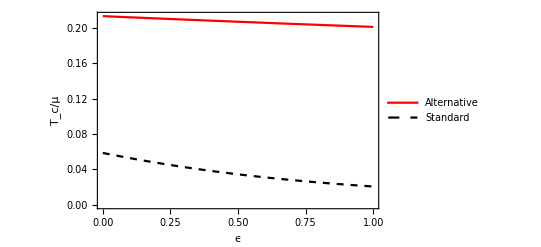

```mathematica
ListLinePlot[{TcO1,TcO2},PlotStyle->{{Red},{Black,Dashed}},LabelStyle->Directive[Black,FontFamily->"Times New Roman",12],PlotLegends->Placed[LineLegend[{"Alternative","Standard"},LegendFunction->Panel],{0.8,0.5}],Frame->True,FrameLabel->{Style["ϵ",14],Style["T_c/μ",14]},RotateLabel->False]
```

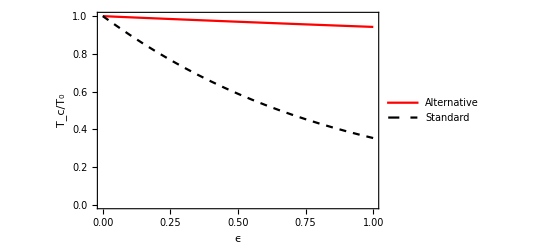

```mathematica
ListLinePlot[{nTcO1,nTcO2},PlotStyle->{{Red},{Black,Dashed}},LabelStyle->Directive[Black,FontFamily->"Times New Roman",12],PlotLegends->Placed[LineLegend[{"Alternative","Standard"},LegendFunction->Panel],{0.8,0.2}],Frame->True,FrameLabel->{Style["ϵ",14],Style["T_c/T_0",14]},RotateLabel->False]
```